```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Recruit function for local and remote pops in the local habitat (1)*)
```

```mathematica
recruitgen = rmax*Exp[-(z-θ1)^2/(2*(τ^2))]
```

ⅇ^(-(z-θ1)^2/(2 τ^2)) rmax

```mathematica
(*recruit = (rmax*τ)/(√(σ^2+τ^2))*Exp[-(θ1-(((1-m)*N1)/((1-m)*N1+m*N2)μ1+(m*N2)/((1-m)*N1+m*N2)μ2))^2/(2*(σ^2+τ^2))];*)
```

```mathematica
RecruitPDF = Integrate[2(((1-m)*N1)/((1-m)*N1+m*N2)*PDF[NormalDistribution[μ1,σ],y]+(m*N2)/((1-m)*N1+m*N2)*PDF[NormalDistribution[μ2,σ],y])*(((1-m)*N1)/((1-m)*N1+m*N2)*PDF[NormalDistribution[μ1,σ],2*z-y]+(m*N2)/((1-m)*N1+m*N2)*PDF[NormalDistribution[μ2,σ],2*z-y]),{y,-Infinity,Infinity}]
```

$Aborted

```mathematica
RecruitPDFsimple=1/(((-1+m) N1-m N2)^2 √π)ⅇ^(-(2 z^2+2 μ1^2+μ1 μ2+2 μ2^2)/(2 σ^2)) (ⅇ^((4 z μ1+μ2 (μ1+2 μ2))/(2 σ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 z (μ1+μ2)+3 (μ1^2+μ2^2))/(4 σ^2)) (-1+m) m N1 N2+ⅇ^((2 μ1^2+4 z μ2+μ1 μ2)/(2 σ^2)) m^2 N2^2) √(1/σ^2);
```

```mathematica
RecruitPDF2 = (recruitgen*RecruitPDFsimple)/Integrate[recruitgen*RecruitPDFsimple,{z,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+μ2^2/σ^2-(2 z^2+2 μ1^2+μ1 μ2+2 μ2^2)/(2 σ^2)-(z-θ1)^2/(2 τ^2)+θ1^2/(σ^2+2 τ^2)) (ⅇ^((4 z μ1+μ2 (μ1+2 μ2))/(2 σ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 z (μ1+μ2)+3 (μ1^2+μ2^2))/(4 σ^2)) (-1+m) m N1 N2+ⅇ^((2 μ1^2+4 z μ2+μ1 μ2)/(2 σ^2)) m^2 N2^2) √(2/σ^2+1/τ^2))/((ⅇ^((μ1 μ2)/(2 σ^2)+μ2^2/σ^2+(2 θ1 μ1)/(σ^2+2 τ^2)+(2 μ1^2 τ^2)/(σ^4+2 σ^2 τ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 θ1 (μ1+μ2) σ^2+4 μ1 μ2 τ^2+μ1^2 (3 σ^2+8 τ^2)+μ2^2 (3 σ^2+8 τ^2))/(4 σ^2 (σ^2+2 τ^2))) (-1+m) m N1 N2+ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+(2 μ2 (θ1 σ^2+μ2 τ^2))/(σ^4+2 σ^2 τ^2)) m^2 N2^2) √(2 π)),Re[1/σ^2+1/(2 τ^2)]≥0]

```mathematica
RecruitPDF2simple =(ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+μ2^2/σ^2-(2 z^2+2 μ1^2+μ1 μ2+2 μ2^2)/(2 σ^2)-(z-θ1)^2/(2 τ^2)+θ1^2/(σ^2+2 τ^2)) (ⅇ^((4 z μ1+μ2 (μ1+2 μ2))/(2 σ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 z (μ1+μ2)+3 (μ1^2+μ2^2))/(4 σ^2)) (-1+m) m N1 N2+ⅇ^((2 μ1^2+4 z μ2+μ1 μ2)/(2 σ^2)) m^2 N2^2) √(2/σ^2+1/τ^2))/((ⅇ^((μ1 μ2)/(2 σ^2)+μ2^2/σ^2+(2 θ1 μ1)/(σ^2+2 τ^2)+(2 μ1^2 τ^2)/(σ^4+2 σ^2 τ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 θ1 (μ1+μ2) σ^2+4 μ1 μ2 τ^2+μ1^2 (3 σ^2+8 τ^2)+μ2^2 (3 σ^2+8 τ^2))/(4 σ^2 (σ^2+2 τ^2))) (-1+m) m N1 N2+ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+(2 μ2 (θ1 σ^2+μ2 τ^2))/(σ^4+2 σ^2 τ^2)) m^2 N2^2) √(2 π));
```

```mathematica
Integrate[RecruitPDF2simple,{z,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(-μ1^2/σ^2-(μ1 μ2)/(2 σ^2)-μ2^2/σ^2-θ1^2/(σ^2+2 τ^2)) (ⅇ^((μ1 μ2)/(2 σ^2)+μ2^2/σ^2+(2 θ1 μ1)/(σ^2+2 τ^2)+(2 μ1^2 τ^2)/(σ^4+2 σ^2 τ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 θ1 (μ1+μ2) σ^2+4 μ1 μ2 τ^2+μ1^2 (3 σ^2+8 τ^2)+μ2^2 (3 σ^2+8 τ^2))/(4 σ^2 (σ^2+2 τ^2))) (-1+m) m N1 N2+ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+(2 μ2 (θ1 σ^2+μ2 τ^2))/(σ^4+2 σ^2 τ^2)) m^2 N2^2) √(1/σ^2) √(1/τ^2))/(((-1+m) N1-m N2)^2 √π √(2/σ^2+1/τ^2)),Re[1/σ^2+1/(2 τ^2)]≥0]

```mathematica
NR=(Recruitdist2simple)*((1-m)*N1+m*N2)*Exp[-β*((1-m)*N1+m*N2)];
```

```mathematica
recruitmean = Integrate[z*RecruitPDFsimple,{z,-Infinity,Infinity}]
```

ConditionalExpression[(N1 μ1-m N1 μ1+m N2 μ2)/(N1-m N1+m N2),Re[σ^2]≥0]

```mathematica
recruitvar = Integrate[z^2*RecruitPDFsimple,{z,-Infinity,Infinity}]-  Integrate[z*RecruitPDFsimple,{z,-Infinity,Infinity}]^2
```

ConditionalExpression[-(N1 μ1-m N1 μ1+m N2 μ2)^2/(N1-m N1+m N2)^2+((-1+m)^2 N1^2 (2 μ1^2+σ^2)+m^2 N2^2 (2 μ2^2+σ^2)-(-1+m) m N1 N2 ((μ1+μ2)^2+2 σ^2))/(2 ((-1+m) N1-m N2)^2),Re[σ^2]≥0]

```mathematica
recruitmeansimple = (N1 μ1-m N1 μ1+m N2 μ2)/(N1-m N1+m N2);
recruitvarsimple = -(N1 μ1-m N1 μ1+m N2 μ2)^2/(N1-m N1+m N2)^2+((-1+m)^2 N1^2 (2 μ1^2+σ^2)+m^2 N2^2 (2 μ2^2+σ^2)-(-1+m) m N1 N2 ((μ1+μ2)^2+2 σ^2))/(2 ((-1+m) N1-m N2)^2);
```

```mathematica
FullSimplify[(N1 μ1-m N1 μ1+m N2 μ2)^2/(N1-m N1+m N2)^2+((-1+m)^2 N1^2 (2 μ1^2+σ^2)+m^2 N2^2 (2 μ2^2+σ^2)-(-1+m) m N1 N2 ((μ1+μ2)^2+2 σ^2))/(2 ((-1+m) N1-m N2)^2)]
```

((-1+m)^2 N1^2 (4 μ1^2+σ^2)+m^2 N2^2 (4 μ2^2+σ^2)-(-1+m) m N1 N2 (μ1^2+6 μ1 μ2+μ2^2+2 σ^2))/(2 (N1-m N1+m N2)^2)

```mathematica
NextGenTraitPDF =RecruitPDF2simple;
NormApprox=PDF[NormalDistribution[((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +σ^2*(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2),σ],z];
```

```mathematica
(*Calculate the mean and variance of the NextGenTraitPDF*)
```

```mathematica
ngmean = Integrate[z*NextGenTraitPDF,{z,-Infinity,Infinity}]
ngvar =  Integrate[z^2*NextGenTraitPDF,{z,-Infinity,Infinity}]-  Integrate[z*NextGenTraitPDF,{z,-Infinity,Infinity}]^2
```

ConditionalExpression[(ⅇ^(-(θ1^2 σ^2)/(2 σ^2 τ^2+4 τ^4)) (ⅇ^((μ1 μ2+2 μ2^2+((θ1 σ^2+2 μ1 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) (-1+m)^2 N1^2 (θ1 σ^2+2 μ1 τ^2)+ⅇ^((2 μ1^2+μ1 μ2+((θ1 σ^2+2 μ2 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) m^2 N2^2 (θ1 σ^2+2 μ2 τ^2)-2 ⅇ^((3 μ1^2+3 μ2^2+(2 (θ1 σ^2+(μ1+μ2) τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(4 σ^2)) (-1+m) m N1 N2 (θ1 σ^2+(μ1+μ2) τ^2)))/((ⅇ^((μ1 μ2)/(2 σ^2)+μ2^2/σ^2+(2 θ1 μ1)/(σ^2+2 τ^2)+(2 μ1^2 τ^2)/(σ^4+2 σ^2 τ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 θ1 (μ1+μ2) σ^2+4 μ1 μ2 τ^2+μ1^2 (3 σ^2+8 τ^2)+μ2^2 (3 σ^2+8 τ^2))/(4 σ^2 (σ^2+2 τ^2))) (-1+m) m N1 N2+ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+(2 μ2 (θ1 σ^2+μ2 τ^2))/(σ^4+2 σ^2 τ^2)) m^2 N2^2) (σ^2+2 τ^2)),Re[2/σ^2+1/τ^2]≥0]

ConditionalExpression[-((ⅇ^(-(2 θ1^2 σ^2)/(2 σ^2 τ^2+4 τ^4)) (ⅇ^((μ1 μ2+2 μ2^2+((θ1 σ^2+2 μ1 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) (-1+m)^2 N1^2 (θ1 σ^2+2 μ1 τ^2)+ⅇ^((2 μ1^2+μ1 μ2+((θ1 σ^2+2 μ2 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) m^2 N2^2 (θ1 σ^2+2 μ2 τ^2)-2 ⅇ^((3 μ1^2+3 μ2^2+(2 (θ1 σ^2+(μ1+μ2) τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(4 σ^2)) (-1+m) m N1 N2 (θ1 σ^2+(μ1+μ2) τ^2))^2)/((ⅇ^((μ1 μ2)/(2 σ^2)+μ2^2/σ^2+(2 θ1 μ1)/(σ^2+2 τ^2)+(2 μ1^2 τ^2)/(σ^4+2 σ^2 τ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 θ1 (μ1+μ2) σ^2+4 μ1 μ2 τ^2+μ1^2 (3 σ^2+8 τ^2)+μ2^2 (3 σ^2+8 τ^2))/(4 σ^2 (σ^2+2 τ^2))) (-1+m) m N1 N2+ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+(2 μ2 (θ1 σ^2+μ2 τ^2))/(σ^4+2 σ^2 τ^2)) m^2 N2^2)^2 (σ^2+2 τ^2)^2))+(ⅇ^(-(θ1^2 σ^2)/(2 σ^2 τ^2+4 τ^4)) (ⅇ^((μ1 μ2+2 μ2^2+((θ1 σ^2+2 μ1 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) (-1+m)^2 N1^2 (θ1^2 σ^4+4 θ1 μ1 σ^2 τ^2+σ^4 τ^2+4 μ1^2 τ^4+2 σ^2 τ^4)+ⅇ^((μ2 (μ1+2 μ2)+((θ1 σ^2+2 μ1 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) (-1+m)^2 N1^2 (θ1^2 σ^4+4 θ1 μ1 σ^2 τ^2+σ^4 τ^2+4 μ1^2 τ^4+2 σ^2 τ^4)+2 ⅇ^((2 μ1^2+μ1 μ2+((θ1 σ^2+2 μ2 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) m^2 N2^2 (θ1^2 σ^4+4 θ1 μ2 σ^2 τ^2+σ^4 τ^2+4 μ2^2 τ^4+2 σ^2 τ^4)-4 ⅇ^((3 μ1^2+3 μ2^2+(2 (θ1 σ^2+(μ1+μ2) τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(4 σ^2)) (-1+m) m N1 N2 (θ1^2 σ^4+2 θ1 (μ1+μ2) σ^2 τ^2+τ^2 (σ^4+(μ1+μ2)^2 τ^2+2 σ^2 τ^2))))/(2 (ⅇ^((μ1 μ2)/(2 σ^2)+μ2^2/σ^2+(2 θ1 μ1)/(σ^2+2 τ^2)+(2 μ1^2 τ^2)/(σ^4+2 σ^2 τ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 θ1 (μ1+μ2) σ^2+4 μ1 μ2 τ^2+μ1^2 (3 σ^2+8 τ^2)+μ2^2 (3 σ^2+8 τ^2))/(4 σ^2 (σ^2+2 τ^2))) (-1+m) m N1 N2+ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+(2 μ2 (θ1 σ^2+μ2 τ^2))/(σ^4+2 σ^2 τ^2)) m^2 N2^2) (σ^2+2 τ^2)^2),Re[2/σ^2+1/τ^2]≥0]

```mathematica
ngmeansimple=(ⅇ^(-(θ1^2 σ^2)/(2 σ^2 τ^2+4 τ^4)) (ⅇ^((μ1 μ2+2 μ2^2+((θ1 σ^2+2 μ1 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) (-1+m)^2 N1^2 (θ1 σ^2+2 μ1 τ^2)+ⅇ^((2 μ1^2+μ1 μ2+((θ1 σ^2+2 μ2 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) m^2 N2^2 (θ1 σ^2+2 μ2 τ^2)-2 ⅇ^((3 μ1^2+3 μ2^2+(2 (θ1 σ^2+(μ1+μ2) τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(4 σ^2)) (-1+m) m N1 N2 (θ1 σ^2+(μ1+μ2) τ^2)))/((ⅇ^((μ1 μ2)/(2 σ^2)+μ2^2/σ^2+(2 θ1 μ1)/(σ^2+2 τ^2)+(2 μ1^2 τ^2)/(σ^4+2 σ^2 τ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 θ1 (μ1+μ2) σ^2+4 μ1 μ2 τ^2+μ1^2 (3 σ^2+8 τ^2)+μ2^2 (3 σ^2+8 τ^2))/(4 σ^2 (σ^2+2 τ^2))) (-1+m) m N1 N2+ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+(2 μ2 (θ1 σ^2+μ2 τ^2))/(σ^4+2 σ^2 τ^2)) m^2 N2^2) (σ^2+2 τ^2));
ngvarsimple = -((ⅇ^(-(2 θ1^2 σ^2)/(2 σ^2 τ^2+4 τ^4)) (ⅇ^((μ1 μ2+2 μ2^2+((θ1 σ^2+2 μ1 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) (-1+m)^2 N1^2 (θ1 σ^2+2 μ1 τ^2)+ⅇ^((2 μ1^2+μ1 μ2+((θ1 σ^2+2 μ2 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) m^2 N2^2 (θ1 σ^2+2 μ2 τ^2)-2 ⅇ^((3 μ1^2+3 μ2^2+(2 (θ1 σ^2+(μ1+μ2) τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(4 σ^2)) (-1+m) m N1 N2 (θ1 σ^2+(μ1+μ2) τ^2))^2)/((ⅇ^((μ1 μ2)/(2 σ^2)+μ2^2/σ^2+(2 θ1 μ1)/(σ^2+2 τ^2)+(2 μ1^2 τ^2)/(σ^4+2 σ^2 τ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 θ1 (μ1+μ2) σ^2+4 μ1 μ2 τ^2+μ1^2 (3 σ^2+8 τ^2)+μ2^2 (3 σ^2+8 τ^2))/(4 σ^2 (σ^2+2 τ^2))) (-1+m) m N1 N2+ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+(2 μ2 (θ1 σ^2+μ2 τ^2))/(σ^4+2 σ^2 τ^2)) m^2 N2^2)^2 (σ^2+2 τ^2)^2))+(ⅇ^(-(θ1^2 σ^2)/(2 σ^2 τ^2+4 τ^4)) (ⅇ^((μ1 μ2+2 μ2^2+((θ1 σ^2+2 μ1 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) (-1+m)^2 N1^2 (θ1^2 σ^4+4 θ1 μ1 σ^2 τ^2+σ^4 τ^2+4 μ1^2 τ^4+2 σ^2 τ^4)+ⅇ^((μ2 (μ1+2 μ2)+((θ1 σ^2+2 μ1 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) (-1+m)^2 N1^2 (θ1^2 σ^4+4 θ1 μ1 σ^2 τ^2+σ^4 τ^2+4 μ1^2 τ^4+2 σ^2 τ^4)+2 ⅇ^((2 μ1^2+μ1 μ2+((θ1 σ^2+2 μ2 τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(2 σ^2)) m^2 N2^2 (θ1^2 σ^4+4 θ1 μ2 σ^2 τ^2+σ^4 τ^2+4 μ2^2 τ^4+2 σ^2 τ^4)-4 ⅇ^((3 μ1^2+3 μ2^2+(2 (θ1 σ^2+(μ1+μ2) τ^2)^2)/(τ^2 (σ^2+2 τ^2)))/(4 σ^2)) (-1+m) m N1 N2 (θ1^2 σ^4+2 θ1 (μ1+μ2) σ^2 τ^2+τ^2 (σ^4+(μ1+μ2)^2 τ^2+2 σ^2 τ^2))))/(2 (ⅇ^((μ1 μ2)/(2 σ^2)+μ2^2/σ^2+(2 θ1 μ1)/(σ^2+2 τ^2)+(2 μ1^2 τ^2)/(σ^4+2 σ^2 τ^2)) (-1+m)^2 N1^2-2 ⅇ^((4 θ1 (μ1+μ2) σ^2+4 μ1 μ2 τ^2+μ1^2 (3 σ^2+8 τ^2)+μ2^2 (3 σ^2+8 τ^2))/(4 σ^2 (σ^2+2 τ^2))) (-1+m) m N1 N2+ⅇ^(μ1^2/σ^2+(μ1 μ2)/(2 σ^2)+(2 μ2 (θ1 σ^2+μ2 τ^2))/(σ^4+2 σ^2 τ^2)) m^2 N2^2) (σ^2+2 τ^2)^2);
```

```mathematica
(*Check to see if the NextGen PDf sums to 1*)
```

```mathematica
FullSimplify[NIntegrate[NextGenTraitPDF,{z,-Infinity,Infinity}]]
```

NIntegrate[NextGenTraitPDF,{z,-∞,∞}]

```mathematica
(*Compare Exact and Approximate PDFs*)
```

```mathematica
NormApprox
```

(ⅇ^(-(z-((1-m) N1 μ1)/((1-m) N1+m N2)-(m N2 μ2)/((1-m) N1+m N2))^2/(2 σ^2)))/(√(2 π) σ)

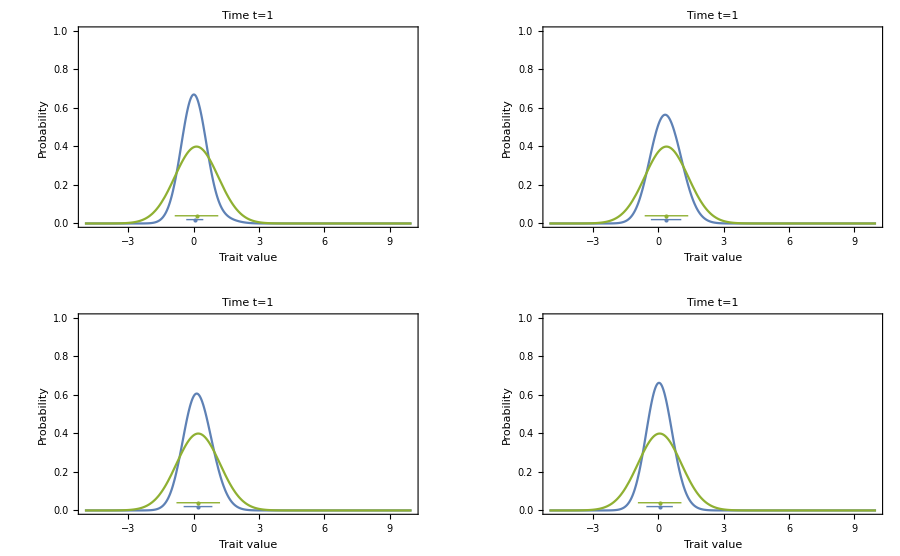

```mathematica
Block[{μ1=0,μ2=4,m=0.1,N1=1000,N2=600,σ=1,β=0.001,τ=1,rmax=2,θ1=0,h=1},
PDF1=Show[{
Plot[NextGenTraitPDF,{z,-5,10},PlotRange->{0,1},PlotStyle->ColorData[97,1],Frame->True,FrameLabel->{Style["Trait value",FontSize->12],Style["Probability",FontSize->14]},PlotLabel->"Time t=1",LabelStyle->Directive[FontSize->12]],
Graphics[{ColorData[97,1],Point[{ngmeansimple,0.02}]}],
Graphics[{ColorData[97,1],Line[{{ngmeansimple-ngvarsimple,0.02},{ngmeansimple+ngvarsimple,0.02}}]}],
Plot[NormApprox,{z,-5,10},PlotStyle->ColorData[97,3]],
Graphics[{ColorData[97,3],Point[{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2),0.04}]}],
Graphics[{ColorData[97,3],Line[{{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2)-1,0.04},{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2)+1,0.04}}]}]
}];
]
Block[{μ1=0,μ2=2,m=0.5,N1=1000,N2=600,σ=1,β=0.001,τ=1,rmax=2,θ1=0,h=1},
PDF2=Show[{
Plot[NextGenTraitPDF,{z,-5,10},PlotRange->{0,1},PlotStyle->ColorData[97,1],Frame->True,FrameLabel->{Style["Trait value",FontSize->12],Style["Probability",FontSize->14]},PlotLabel->"Time t=1",LabelStyle->Directive[FontSize->12]],
Graphics[{ColorData[97,1],Point[{ngmeansimple,0.02}]}],
Graphics[{ColorData[97,1],Line[{{ngmeansimple-Sqrt[ngvarsimple],0.02},{ngmeansimple+Sqrt[ngvarsimple],0.02}}]}],
Plot[NormApprox,{z,-5,10},PlotStyle->ColorData[97,3]],
Graphics[{ColorData[97,3],Point[{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2),0.04}]}],
Graphics[{ColorData[97,3],Line[{{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2)-1,0.04},{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2)+1,0.04}}]}]
}];
]
Block[{μ1=0,μ2=2,m=0.3,N1=1000,N2=600,σ=1,τ=1,rmax=2,θ1=0,h=1},
PDF3=Show[{
Plot[NextGenTraitPDF,{z,-5,10},PlotRange->{0,1},PlotStyle->ColorData[97,1],Frame->True,FrameLabel->{Style["Trait value",FontSize->12],Style["Probability",FontSize->14]},PlotLabel->"Time t=1",LabelStyle->Directive[FontSize->12]],
Graphics[{ColorData[97,1],Point[{ngmeansimple,0.02}]}],
Graphics[{ColorData[97,1],Line[{{ngmeansimple-Sqrt[ngvarsimple],0.02},{ngmeansimple+Sqrt[ngvarsimple],0.02}}]}],
Plot[NormApprox,{z,-5,10},PlotStyle->ColorData[97,3]],
Graphics[{ColorData[97,3],Point[{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2),0.04}]}],
Graphics[{ColorData[97,3],Line[{{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2)-1,0.04},{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2)+1,0.04}}]}]
}];
]
Block[{μ1=0,μ2=2,m=0.2*(1-N1/(1000+N1)),N1=1000,N2=600,σ=1,β=0.001,τ=1,rmax=2,θ1=0,h=1},
PDF4=Show[{
Plot[NextGenTraitPDF,{z,-5,10},PlotRange->{0,1},PlotStyle->ColorData[97,1],Frame->True,FrameLabel->{Style["Trait value",FontSize->12],Style["Probability",FontSize->14]},PlotLabel->"Time t=1",LabelStyle->Directive[FontSize->12]],
Graphics[{ColorData[97,1],Point[{ngmeansimple,0.02}]}],
Graphics[{ColorData[97,1],Line[{{ngmeansimple-Sqrt[ngvarsimple],0.02},{ngmeansimple+Sqrt[ngvarsimple],0.02}}]}],
Plot[NormApprox,{z,-5,10},PlotStyle->ColorData[97,3]],
Graphics[{ColorData[97,3],Point[{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2),0.04}]}],
Graphics[{ColorData[97,3],Line[{{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2)-1,0.04},{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2 +h*σ^2(θ1-((1-m)*N1)/((1-m)*N1+m*N2) μ1-(m*N2)/((1-m)*N1+m*N2) μ2)/(σ^2+τ^2)+1,0.04}}]}]
}];
]
PDFPlot = GraphicsGrid[{{PDF1,PDF2},{PDF3,PDF4}},ImageSize->900]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2017_SalmonStrays/Manuscript/FinalDraft3/fig_PDF.pdf"}],PDFPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/Manuscript/FinalDraft3/fig_PDF.pdf

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 2-50 ⅇ^625 √π+50 ⅇ^625 √π Erf[25].

General::stop: Further output of N::meprec will be suppressed during this calculation.

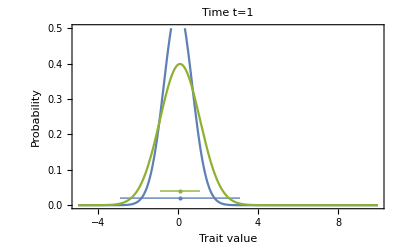

```mathematica
Block[{μ1=0,μ2=50,m=0.004,N1=1000,N2=500,σ=1,Z=0.5,β=0.001,τ=1,rmax=2,θ1=0},
Show[{
Plot[NextGenTraitPDF,{z,-5,10},PlotRange->{0,0.5},PlotStyle->ColorData[97,1],Frame->True,FrameLabel->{Style["Trait value",FontSize->12],Style["Probability",FontSize->14]},PlotLabel->"Time t=1",LabelStyle->Directive[FontSize->12]],
Graphics[{ColorData[97,1],Point[{ngmeansimple,0.02}]}],
Graphics[{ColorData[97,1],Line[{{ngmeansimple-ngvarsimple,0.02},{ngmeansimple+ngvarsimple,0.02}}]}],
Plot[NormApprox,{z,-5,10},PlotStyle->ColorData[97,3]],
Graphics[{ColorData[97,3],Point[{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2,0.04}]}],
Graphics[{ColorData[97,3],Line[{{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2-1,0.04},{((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2+1,0.04}}]}]
}]
]
```

```mathematica
(*Where m is density dependent*)
(*It is an even better approximation*)
```

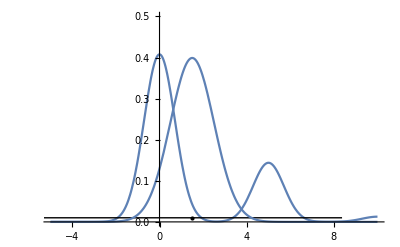

```mathematica
Block[{μ1=0,μ2=10,m=0.3*(1-N1/(1000+N1)),N1=1000,N2=1000,σ=1,Z=0.5,β=0.001,τ=1,rmax=2,θ1=1},
Show[{
Plot[NextGenTraitPDF,{z,-5,10},PlotRange->{0,0.5}],
Graphics[Point[{ngmeansimple,0.01}]],
Graphics[Line[{{ngmeansimple-ngvarsimple,0.01},{ngmeansimple+ngvarsimple,0.01}}]],
Plot[NormApprox,{z,-5,10}]
}]
]
```

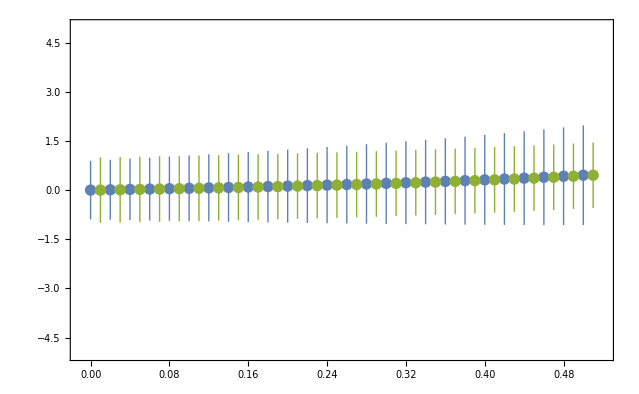

```mathematica
Block[{μ1=0,μ2=5,N1=1000,N2=100,σ=1,Z=0.5,β=0.001,τ=1,rmax=2,θ1=1},
mvec=Table[m,{m,0,0.5,0.02}];
MeanMRMD=Table[{m,ngmeansimple},{m,mvec}];
VarMRMD={Table[{m,ngmeansimple-Sqrt[ngvarsimple]},{m,mvec}],Table[{m,ngmeansimple+Sqrt[ngvarsimple]},{m,mvec}]};
MeanNorm = Table[{m+0.01,((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2},{m,mvec}];
(*MeanNorm[[3,1]]*)
VarNorm = σ^2;
Show[{
ListPlot[MeanMRMD,PlotRange->{{-0.01,0.52},{-5,5}},Frame->True],
Table[Graphics[{ColorData[97,1],Line[{VarMRMD[[1,i]],VarMRMD[[2,i]]}]}],{i,1,Length[mvec]}],
Table[Graphics[{ColorData[97,3],Line[{{mvec[[i]]+0.01,MeanNorm[[i,2]]-σ},{mvec[[i]]+0.01,MeanNorm[[i,2]]+σ}}]}],{i,1,Length[mvec]}],
ListPlot[MeanNorm,PlotStyle->ColorData[97,3]]
}]
]
```

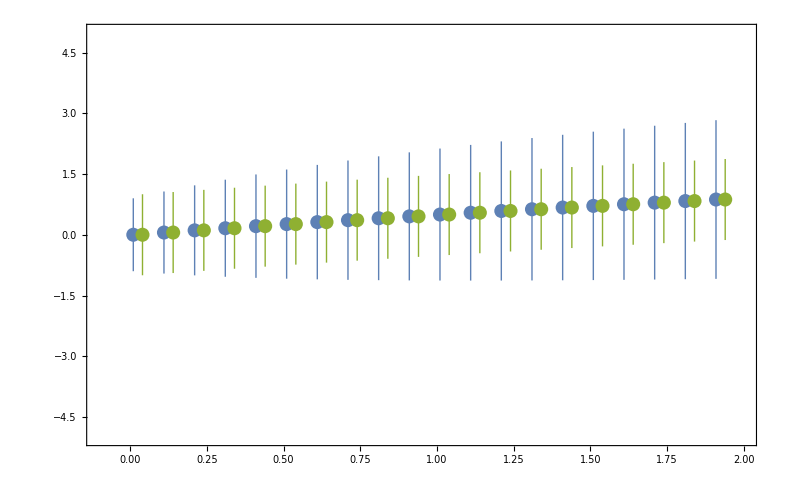

```mathematica
Block[{μ1=0,μ2=5,N1=1000,N2=N1*R,m=0.1,σ=1,Z=0.5,β=0.001,τ=1,rmax=2,θ1=1},
Rvec=Table[R,{R,0.01,2,0.1}];
offset=0.03;
MeanMRMD=Table[{R,ngmeansimple},{R,Rvec}];
VarMRMD={Table[{R,ngmeansimple-Sqrt[ngvarsimple]},{R,Rvec}],Table[{R,ngmeansimple+Sqrt[ngvarsimple]},{R,Rvec}]};
MeanNorm = Table[{R+offset,((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2},{R,Rvec}];

VarNorm = σ^2;
Show[{
ListPlot[MeanMRMD,PlotRange->{{-0.1,2},{-5,5}},Frame->True],
Table[Graphics[{ColorData[97,1],Line[{VarMRMD[[1,i]],VarMRMD[[2,i]]}]}],{i,1,Length[Rvec]}],
Table[Graphics[{ColorData[97,3],Line[{{Rvec[[i]]+offset,MeanNorm[[i,2]]-σ},{Rvec[[i]]+offset,MeanNorm[[i,2]]+σ}}]}],{i,1,Length[Rvec]}],
ListPlot[MeanNorm,PlotStyle->ColorData[97,3]]
}]
]
```

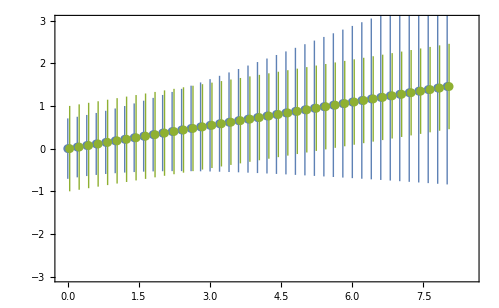

```mathematica
Block[{μ1=0,μ2=0+d,N1=500,N2=1000,m=0.1,σ=1,Z=1000,β=0.001,τ=1,rmax=2,θ1=1},
dvec=Table[d,{d,0.0,8,0.2}];
offset=0.04;
MeanMRMD=Table[{d,ngmeansimple},{d,dvec}];
VarMRMD={Table[{d,ngmeansimple-Sqrt[ngvarsimple]},{d,dvec}],Table[{d,ngmeansimple+Sqrt[ngvarsimple]},{d,dvec}]};
MeanNorm = Table[{d+offset,((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2},{d,dvec}];

VarNorm = σ^2;
Show[{
ListPlot[MeanMRMD,PlotRange->{{-0.1,8.5},{-3,3}},Frame->True],
Table[Graphics[{ColorData[97,1],Line[{VarMRMD[[1,i]],VarMRMD[[2,i]]}]}],{i,1,Length[dvec]}],
Table[Graphics[{ColorData[97,3],Line[{{dvec[[i]]+offset,MeanNorm[[i,2]]-σ},{dvec[[i]]+offset,MeanNorm[[i,2]]+σ}}]}],{i,1,Length[dvec]}],
ListPlot[MeanNorm,PlotStyle->ColorData[97,3]]
}]
]
```

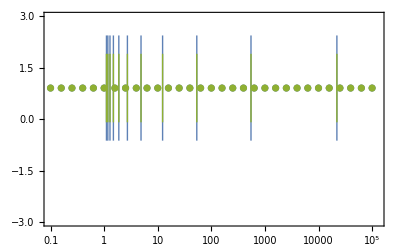

```mathematica
Block[{μ1=0,μ2=5,N1=500,N2=1000,m=0.1,σ=1,β=0.001,τ=1,rmax=2,θ1=1},
zvec=Table[10^Z,{Z,-1,5,0.2}];
offset=0.0;
MeanMRMD=Table[{Z,ngmeansimple},{Z,zvec}];
VarMRMD={Table[{Z,ngmeansimple-Sqrt[ngvarsimple]},{Z,zvec}],Table[{Z,ngmeansimple+Sqrt[ngvarsimple]},{Z,zvec}]};
MeanNorm = Table[{Z+offset,((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2},{Z,zvec}];

VarNorm = σ^2;
Show[{
ListLogLinearPlot[MeanMRMD,PlotRange->{{0.1,10^5.1},{-3,3}},Frame->True],
Table[Graphics[{ColorData[97,1],Line[{VarMRMD[[1,i]],VarMRMD[[2,i]]}]}],{i,1,Length[zvec]}],
Table[Graphics[{ColorData[97,3],Line[{{zvec[[i]]+offset,MeanNorm[[i,2]]-σ},{zvec[[i]]+offset,MeanNorm[[i,2]]+σ}}]}],{i,1,Length[zvec]}],
ListLogLinearPlot[MeanNorm,PlotStyle->ColorData[97,3]]
}]
]
```

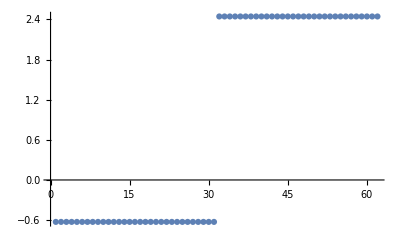

```mathematica
ListPlot[Flatten[VarMRMD,1][[All,2]]]
```

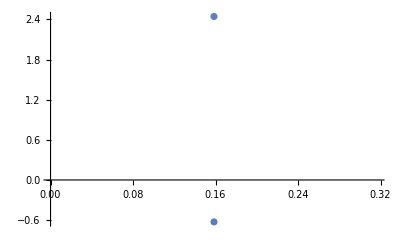

```mathematica
ListPlot[VarMRMD[[All,2]]]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2017_SalmonStrays/manuscript/FinalDraft_rev/fig_contSD.pdf"}],CPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/FinalDraft_rev/fig_contSD.pdf

```mathematica
Block[{μ1=0,μ2=5,N1=1000,N2=N1*R,σ=1,Z=0.5,β=0.001,τ=1,rmax=2,θ1=1},
Rvec=Table[R,{R,0.0,5,0.1}];
mvec=Table[m,{m,0.0,0.5,0.01}];
offset=0.1;
VarMRMD=Flatten[Table[{m,R,Sqrt[ngvarsimple]},{m,mvec},{R,Rvec}],1];

VarNorm = σ^2;
P1=
ListContourPlot[VarMRMD,Contours->20,PlotRange->{0.0,5},PlotLegends->BarLegend[{Automatic,Automatic},LegendMarkerSize->175],FrameLabel->{"m","N_j/N_i"},PlotLabel->"Δθ=5"];
]
Block[{μ1=0,μ2=8,N1=1000,N2=N1*R,σ=1,Z=0.5,β=0.001,τ=1,rmax=2,θ1=1},
Rvec=Table[R,{R,0.01,5,0.1}];
mvec=Table[m,{m,0.01,0.5,0.01}];
offset=0.1;
VarMRMD=Flatten[Table[{m,R,Sqrt[ngvarsimple]},{m,mvec},{R,Rvec}],1];
VarNorm = σ^2;
P2=
ListContourPlot[VarMRMD,Contours->20,PlotRange->{0.0,5},PlotLegends->BarLegend[{Automatic,Automatic},LegendMarkerSize->175],FrameLabel->{"m","N_j/N_i"},PlotLabel->"Δθ=8"];
]
(*For density dependent m*)
Block[{μ1=0,μ2=5,N1=1000,m=m0*(1-N1/(1000+N1)),N2=N1*R,σ=1,Z=0.5,β=0.001,τ=1,rmax=2,θ1=1},
Rvec=Table[R,{R,0.0,5,0.1}];
mvec=Table[m0,{m0,0.0,0.5,0.01}];
offset=0.1;
VarMRMD=Flatten[Table[{m0,R,Sqrt[ngvarsimple]},{m0,mvec},{R,Rvec}],1];

VarNorm = σ^2;
P1m=
ListContourPlot[VarMRMD,Contours->20,PlotRange->{0.0,5},PlotLegends->BarLegend[{Automatic,Automatic},LegendMarkerSize->175],FrameLabel->{"m_0","N_j/N_i"},PlotLabel->"Δθ=5"];
]
Block[{μ1=0,μ2=8,N1=1000,m=m0*(1-N1/(1000+N1)),N2=N1*R,σ=1,Z=0.5,β=0.001,τ=1,rmax=2,θ1=1},
Rvec=Table[R,{R,0.01,5,0.1}];
mvec=Table[m0,{m0,0.01,0.5,0.01}];
offset=0.1;
VarMRMD=Flatten[Table[{m0,R,Sqrt[ngvarsimple]},{m0,mvec},{R,Rvec}],1];
VarNorm = σ^2;
P2m=
ListContourPlot[VarMRMD,Contours->20,PlotRange->{0.0,5},PlotLegends->BarLegend[{Automatic,Automatic},LegendMarkerSize->175],FrameLabel->{"m_0","N_j/N_i"},PlotLabel->"Δθ=8"];
]
CPlot=GraphicsGrid[{{P1,P2},{P1m,P2m}},ImageSize->500]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2017_SalmonStrays/manuscript/FinalDraft_rev/fig_contSD.pdf"}],CPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2017_SalmonStrays/manuscript/FinalDraft_rev/fig_contSD.pdf

```mathematica
(*Timestep t=2*)
```

```mathematica
recruit11 = (rmax*τ)/(√(σ^2+τ^2))*Exp[-(θ1-μ1)^2/(2*(σ^2+τ^2))];
recruit12 = (rmax*τ)/(√(σ^2+τ^2))*Exp[-(θ1-μ2)^2/(2*(σ^2+τ^2))];
recruit21 = (rmax*τ)/(√(σ^2+τ^2))*Exp[-(θ2-μ2)^2/(2*(σ^2+τ^2))];
recruit22 = (rmax*τ)/(√(σ^2+τ^2))*Exp[-(θ2-μ1)^2/(2*(σ^2+τ^2))];
RecruitPDF1 = Integrate[2(((1-m)*N1)/((1-m)*N1+m*N2)*PDF[NormalDistribution[μ1,σ],y]+(m*N2)/((1-m)*N1+m*N2)*PDF[NormalDistribution[μ2,σ],y])*(((1-m)*N1)/((1-m)*N1+m*N2)*PDF[NormalDistribution[μ1,σ],2*z-y]+(m*N2)/((1-m)*N1+m*N2)*PDF[NormalDistribution[μ2,σ],2*z-y]),{y,-Infinity,Infinity}];
RecruitPDF2 = Integrate[2(((1-m)*N2)/((1-m)*N2+m*N1)*PDF[NormalDistribution[μ2,σ],y]+(m*N1)/((1-m)*N2+m*N1)*PDF[NormalDistribution[μ1,σ],y])*(((1-m)*N2)/((1-m)*N2+m*N1)*PDF[NormalDistribution[μ2,σ],2*z-y]+(m*N1)/((1-m)*N2+m*N1)*PDF[NormalDistribution[μ1,σ],2*z-y]),{y,-Infinity,Infinity}];
NR1=((1-m)*N1*recruit11 + m*N2*recruit12)*Exp[-β*((1-m)*N1+m*N2)];
NR2=((1-m)*N2*recruit21 + m*N2*recruit22)*Exp[-β*((1-m)*N1+m*N2)];
p11 = ((1-m)*N1*Exp[-Z])/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
p12 = (m*N2*Exp[-Z])/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
p13=NR/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
p21 = ((1-m)*N1*Exp[-Z])/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
p22 = (m*N2*Exp[-Z])/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
p23=NR/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
NextGenTraitPDF1 = p11*PDF[NormalDistribution[μ1,σ],z]+p12*PDF[NormalDistribution[μ2,σ],z]+(1-p11-p12)*RecruitPDFsimple1;
NextGenTraitPDF2 = p21*PDF[NormalDistribution[μ2,σ],z]+p22*PDF[NormalDistribution[μ1,σ],z]+(1-p21-p22)*RecruitPDFsimple2;
RecruitPDF1t2 = Integrate[2(((1-m)*N1)/((1-m)*N1+m*N2)*(NextGenTraitPDF1/.z->y) +(m*N2)/((1-m)*N1+m*N2)*(NextGenTraitPDF2/.z->y) )*(((1-m)*N1)/((1-m)*N1+m*N2)*(NextGenTraitPDF1/.z->2*z-y)+(m*N2)/((1-m)*N1+m*N2)*(NextGenTraitPDF2/.z->2*z-y)),{y,-Infinity,Infinity}];
RecruitPDF2t2 = Integrate[2(((1-m)*N2)/((1-m)*N2+m*N1)*(NextGenTraitPDF2/.z->y) +(m*N1)/((1-m)*N2+m*N1)*(NextGenTraitPDF1/.z->y) )*(((1-m)*N2)/((1-m)*N2+m*N1)*(NextGenTraitPDF2/.z->2*z-y)+(m*N1)/((1-m)*N2+m*N1)*(NextGenTraitPDF1/.z->2*z-y)),{y,-Infinity,Infinity}];
newtraitmean1 = ((1-m)*N1)/((1-m)*N1+m*N2)*μ1+(m*N2)/((1-m)*N1+m*N2)*μ2;
newtraitmean2 = ((1-m)*N2)/((1-m)*N2+m*N1)*μ2+(m*N1)/((1-m)*N2+m*N1)*μ1;
NR1t2=((1-m)*N1*recruit11 + m*N2*recruit12)*Exp[-β*((1-m)*N1+m*N2)];
NR2t2=((1-m)*N2*recruit21 + m*N2*recruit22)*Exp[-β*((1-m)*N1+m*N2)];
p11 = ((1-m)*N1*Exp[-Z])/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
p12 = (m*N2*Exp[-Z])/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
p13=NR/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
p21 = ((1-m)*N1*Exp[-Z])/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
p22 = (m*N2*Exp[-Z])/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
p23=NR/((1-m)*N1*Exp[-Z]+m*N2*Exp[-Z]+NR);
NextGenTraitPDF1t2 = p11*PDF[NormalDistribution[μ1,σ],z]+p12*PDF[NormalDistribution[μ2,σ],z]+(1-p11-p12)*RecruitPDFsimple1;
```